# Name:

Show an appropriate amount of work.

Compute magnitude and argument for all possible values of  
z=(ⅈ/(√(1+ⅈ)))^3              
 abs(z_1)=                                                abs(z_2)=                                           
 arg(z_1)=                                                 arg(z_2)=

The roots of z^2+2 ⅈ z+5=0 are 
 z_1=                                           +ⅈ                                            
 z_2=                                           +ⅈ

ⅈ^-ⅈ=                                           +ⅈ                                            
      =                                           ⅇ^

Sketch Points

Sketch the set of points C_1 that satisfy |z-ⅈ|<2. Label the set C_1

Sketch the set of points C_2 that satisfy re(z-2+ⅈ)=4. Label the set C_2

Sketch the set of points C_3 that satisfy arg(z-ⅈ-1)=-π/4. Label the set C_3

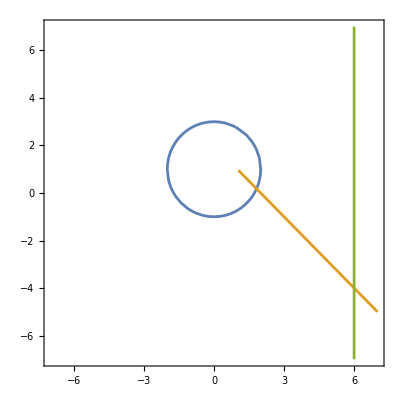

```mathematica
ComplexContourPlot[{
Abs[z-ⅈ]==2,
Arg[z-ⅈ-1]==-π/4,
Re[z-2+ⅈ]==4
},{z,7},
Axes->True]
```

For f(z)=u(x,y)+ⅈ v(x,y) and write down the CR equations
                                             and

For 2 x+ⅈ x^3+2 ⅈ y-3 x^2 y-3 ⅈ x y^2+y^3 complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No                                              .  
If yes f(z)=

Is sin(x-ⅈ y) analytic? Yes or No                                              .  Show any needed work.

Label poles with P_1,P_2,… Label zeros with Z_1,Z_2,… 
Res(f,P_1)=                                             Res(f,P_2)=                                             
Res(f,P_3)=

```mathematica
f[z_]:=3(z-1+ⅈ)/((1-z^2)(ⅈ+2z))
ComplexPlot3D[ f[z],{z,2},PlotLegends->Automatic,
AxesLabel->{"re(z)","im(z)","|f(z)|"}]
```

-Graphics3D-

Complete the following.  The TS log(ⅈ+z)=∑_(k=0)^∞ a_k z^k where a_k=                                                             converges for                                                              . Justify your convergence statement using a Calculus II theorem.   Give a simpler complex analytic justification below.

Label and explain the singularity and color discontinuity visible for log(ⅈ/2+z) in the plot below using appropriate language. The radius of convergence for the TS f(z)=∑_(k=0)^∞ (a_k(z-z_0))^k with z_0==1  is R=                                                             . Explain how you know and explain what the TS converges to around the color discontinuity.

```mathematica
f[z_]:=Log[ⅈ/2+z]
ComplexPlot3D[ f[z],{z,2},PlotLegends->Automatic,
AxesLabel->{"re(z)","im(z)","|f(z)|"}]
```

-Graphics3D-

For the closed CCW contour Γ shown below 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt.
For f(z)=z^2 evaluate ∫_Γ f(z)dz=                                                  and ∫_Γ_2 f(z)dz=                                                 .  Show appropriate work below.

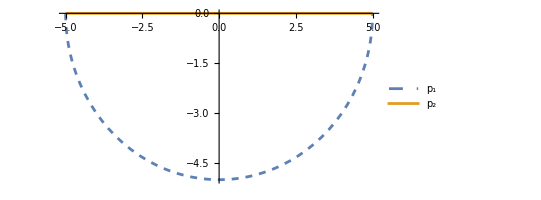

```mathematica
p1[t_]:=5 E^(π ⅈ + π ⅈ t)
p2[t_]:=-5+10 t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]]},{t,0,1},PlotLegends->{"p_1","p_2"},PlotStyle->{Dashed,Dashed[0]}]
```

Compute ∫_Γ ⅇ^z/((z^2+2z+1)(z+ⅈ))dz=                                                             for the CCW contour Γ. Show appropriate work.

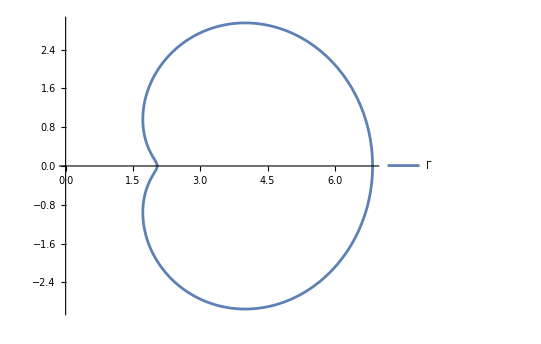

```mathematica
p1[t_]:=2+(E^(2π ⅈ t)+1.2)^2
ParametricPlot[ReIm[p1[t]],{t,0,1},PlotLegends->{"Γ"},
AxesOrigin->{0,0}]
```